# Complex Variables Mathematical Toolbox

## Nathan Yee

## Importing the library

To use the library in any Mathematica notebook, I simply need to write the following lines

```mathematica
SetDirectory[NotebookDirectory[]];
<<complexToolkit.m
```

Next let's test the the library - use ?

```mathematica
?fSpace
```

fSpace[min, max, steps, Log] gives (default) log spaced points from min to max over a given number of points

or press ctr + shift + K to auto complete

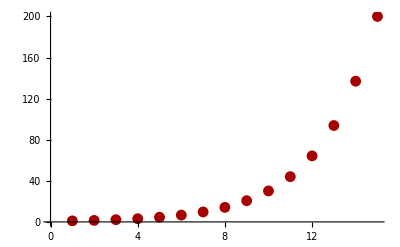

```mathematica
ListPlot[fSpace[1, 200, 15, Log]]
```

Library contains 29 functions

## Newton’s Method

Newton’s Method is a method that successively approximates the roots of a function given an initial guess x_0. The general form of the method is as follows: x_(n+1)=x_n-(f(x_n))/(f'(x_n))

To visualize what Newton’s Method, we will apply it to the complex function z^3-1. Which has roots at:

{z==1.,z==-0.5-0.866025 ⅈ,z==-0.5+0.866025 ⅈ}

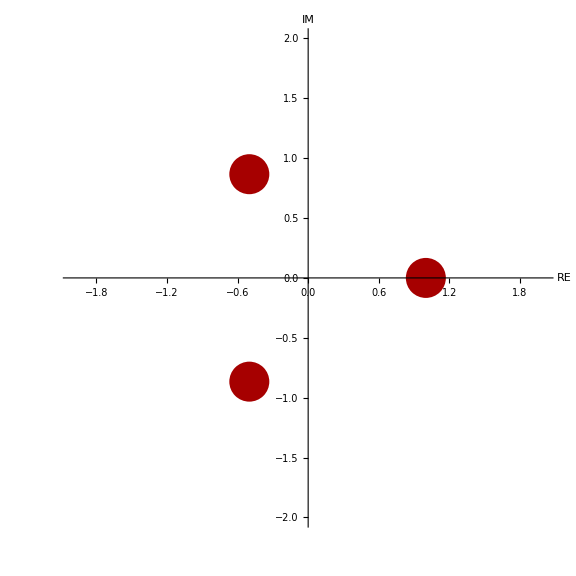

```mathematica
roots=N@Solve[z^3-1==0,{z∈Complexes}];
Flatten[roots/.Rule->Equal]//TraditionalForm
ListPlot[{Re[#],Im[#]}&/@(z/.roots),AspectRatio->1,PlotRange->{{-2,2},{-2,2}},PlotStyle->PointSize[.05],ImageSize->Large,AxesLabel->{"RE","IM"}]
```

If we successively the complex mapping resulting from Newton’s Method, all points should collapse into the roots of the function.

Define function f(z)=z^3-1

```mathematica
f[z_]:=z^3-1
```

Use definition of Newton’s Method to derive mapping function

```mathematica
map=(z-f[z]/f'[z]);
```

Make a circular grid:

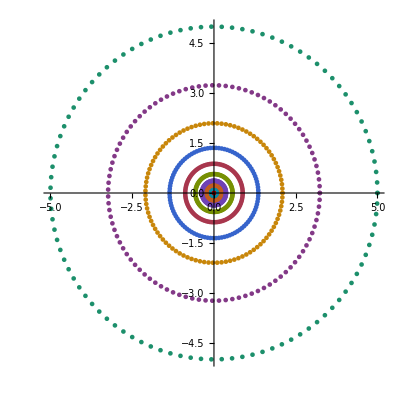

```mathematica
smallestRadius=.1;
largestRadius=5;
numberOfCircles=10;
pointsPerCircle=100;
circleGrid = makeExponentialSpacedCirclePoints[smallestRadius,largestRadius,numberOfCircles,pointsPerCircle];
circleGridCopy1=circleGrid;
ListPlot[circleGridCopy1,AspectRatio->1,PlotRange->Full]
```

```mathematica
makeNewtonMethodAnimation[5,map,35,circleGrid]
```

Take smaller steps

```mathematica
map2=(z-.1 f[z]/f'[z]);
```

```mathematica
?makeNewtonMethodAnimation
```

makeNewtonMethodAnimation[plotRange,map,depth,points] makes animation of successive mappings

```mathematica
makeNewtonMethodAnimation[5,map2,70,circleGrid]
```

Lets try something crazy - live coding demo

Define a new function

```mathematica
g[z_]:=
```

```mathematica
map3=(z-g[z]/g'[z])
```

```mathematica
makeNewtonMethodAnimation[5,map3,100,circleGrid]
```

## Ploting Image Plane

plotImage takes in points, an expression, and a list of colors | returns a plot of the original points and the image points

{RGBColor[0.5, 0.1, 0.7],RGBColor[0.5, 0.3666666666666667, 0.7],RGBColor[0.5, 0.6333333333333333, 0.7],RGBColor[0.5, 0.9, 0.7]}

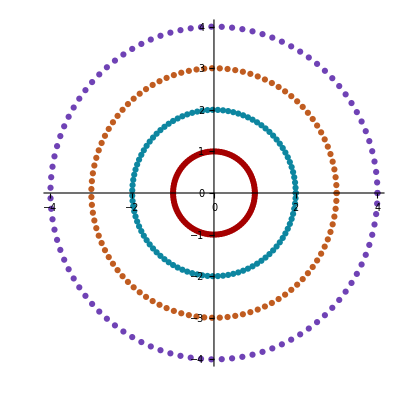

```mathematica
circles=Quiet[makeCirclePoints[1,4,4,100]];
circleColors=makeColorGradient[circles]
ListPlot[circles,AspectRatio->1]
```

No branch cuts (yet) only one rotation around circle

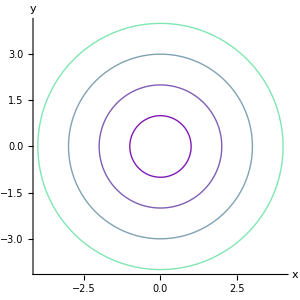
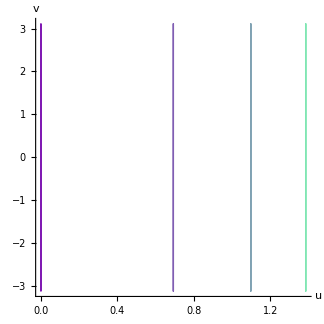
Complex Plane | ImagePlane
-Graphics- | -Graphics-

```mathematica
Quiet@Grid[{{"Complex Plane","ImagePlane"},plotImage[circles,Log[z],Automatic,Automatic,circleColors]}]//TraditionalForm
```

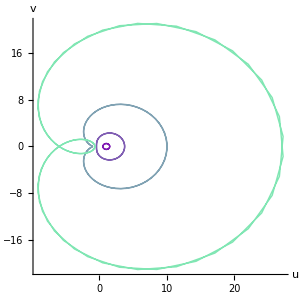
{-Graphics-,-Graphics-}

```mathematica
plotImage[circles,Cos[z],Automatic,All,circleColors]
```

## Grids of lines and stereographic projection

Equal spacing

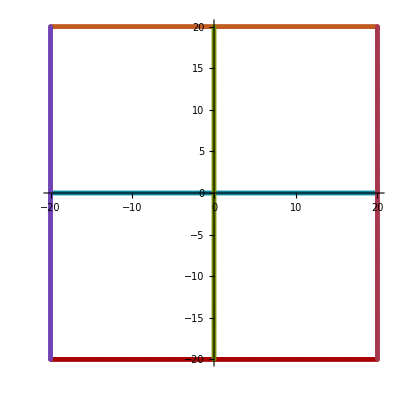

```mathematica
gridPts=makeGridPts[-20,20,300,3];
ListPlot[gridPts,AspectRatio->1]
```

How many points

```mathematica
Times@@Dimensions[gridPts]
```

3600

Stereographic projection to Riemann Sphere

```mathematica
gridPts3D=complexPtsTo3D[gridPts];
ListPointPlot3D[gridPts3D,PlotRange->All,AspectRatio->1,ImageSize->Large]
```

-Graphics3D-

## Grids of lines and stereographic projection

Exponential spacing

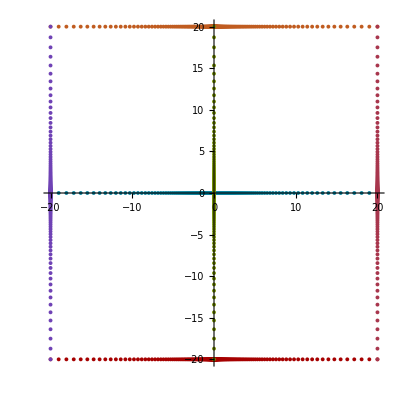

```mathematica
gridPtsLog=makeLogGridPts[-20,20,300,3];
ListPlot[gridPtsLog,AspectRatio->1]
```

How many points

```mathematica
Length[Flatten[gridPtsLog]]
```

3600

Stereographic projection to Riemann Sphere

```mathematica
gridPtsLog3D=complexPtsTo3D[gridPtsLog];
ListPointPlot3D[gridPtsLog3D,PlotRange->All,AspectRatio->1,ImageSize->Large]
```

-Graphics3D-

## Grids of lines and stereographic projection

Spherical spacing

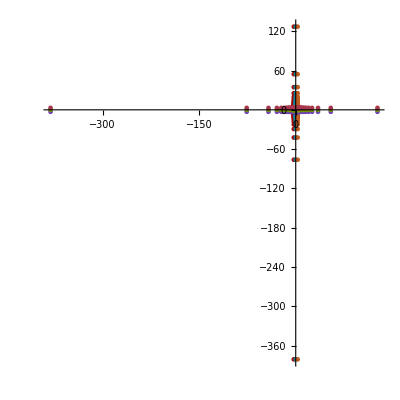

```mathematica
gridPtsSphere=makeGrid[-3,3,300,3];
ListPlot[gridPtsSphere,AspectRatio->1,PlotRange->All]
```

How many points

```mathematica
Length[Flatten[gridPtsSphere]]
```

3600

Stereographic projection to Riemann Sphere

```mathematica
gridPtsSphere3D=complexPtsTo3D[gridPtsSphere];
ListPointPlot3D[gridPtsSphere3D,PlotRange->All,AspectRatio->1,ImageSize->Large]
```

-Graphics3D-

## 3D Printing

```mathematica
object3D=Graphics3D[cylinders[gridPtsSphere3D,.05]];
Rasterize[object3D,RasterSize->1000]
```

-Graphics-

```mathematica
Export["object3D.stl",object3D,{"STL,","BinaryFormat"->True}]
```

object3D.stl

```mathematica
Import["object3D.stl"]
```

-Graphics3D-